Sin[n π]/(n π)

(1-Cos[n π])/(n π)

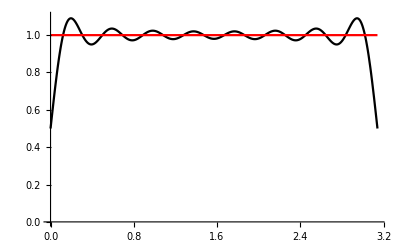

```mathematica
(*Problem #7 part a*)
Clear[a,b,M,x,n,L,f]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,0,L}]*(1/(L))
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,0,L}]*(1/(L))
f[x_]:=1
L:=Pi
a[n]
b[n]

myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

Plot[{Evaluate[myFCos[x,16]+myFSin[x,16]],f[x]},{x,0,L},PlotRange->{0,1.1},PlotStyle->{Black,Red}]
(*Graph of part a f(x) = 1*)
```

(4 n π Cos[n π]+2 (-2+n^2 π^2) Sin[n π])/(n^3 π)

0

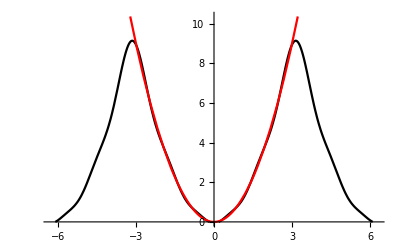

```mathematica
(*Problem #7 part b f(x) = x^2*)
f[x_]:=x^2
L:=Pi
a[n]
b[n]

(*Here is where i form sine and cosing series expansion*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

(*Here is where i form the plot*)
Plot[{Evaluate[myFCos[x,5]+myFSin[x,5]],f[x]},{x,-2L,2L},PlotRange->{0,f[L]+0.5},PlotStyle->{Black,Red}]
(*Graph of part b f(x) = x^2*)
```

(-1+Cos[n π]+n π Sin[n π])/(n^2 π^2)

-(3 (n π Cos[n π]-Sin[n π]))/(n^2 π^2)

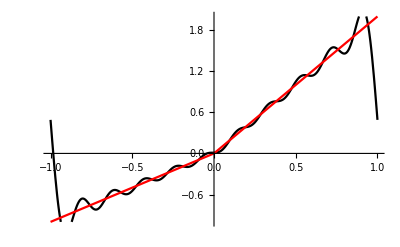

```mathematica
(*Problem #7 part c f(x) is a piecewise defined function*)
f[x_]:=Piecewise[{{x,x>=-L&&x<0},{2x,x>0&&x<=L}}]
L:=1
a[n]
b[n]

(*Here is where i form sine and cosing series expansion*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

(*Here is where i form the plot*)
Plot[{Evaluate[myFCos[x,10]+myFSin[x,10]],f[x]},{x,-L,L},PlotRange->{f[-L],f[L]},PlotStyle->{Black,Red}]
(*Graph of part c f(x) = piecewise*)
(*Notice that the periodicity of the 'x' part and '2x' are 
not the same*)
```

Sin[n π]/(n π)

(1-Cos[n π])/(n π)

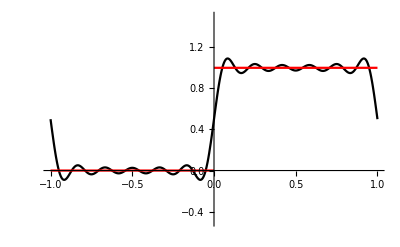

```mathematica
(*Problem #7 part d f(x) is a piecewise defined function*)
f[x_]:=Piecewise[{{0,x>=-L&&x<0},{1,x>0&&x<=L}}]
L:=1
a[n]
b[n]

(*Here is where i form sine and cosing series expansion*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

(*Here is where i form the plot*)
Plot[{Evaluate[myFCos[x,12]+myFSin[x,12]],f[x]},{x,-L,L},PlotRange->{-0.5,1.5},PlotStyle->{Black,Red}]
(*Graph of part d piecewise*)
(*Notice that the graph switches form 0 and 1 at the origin*)
```